```mathematica
SetDirectory[NotebookDirectory[]];
Needs["ErrorBarPlots`"]
```

```mathematica
niceStyle={
Axes->True,
Frame->True,
GridLines->Automatic,
ImageSize->600,
ImageMargins->3,
LabelStyle->{"Arial",16,Bold},
FrameTicksStyle->{Directive[16,Plain],Directive[16,Plain]},
FrameStyle->Thick,
GridLinesStyle->Directive[Dashed,Gray],
AxesStyle->Directive[Thick,Dashed]
};
```

```mathematica
CombineError[daten_,er_]:=Transpose[{daten[[All,1]],daten[[All,2]],Table[er,{Length[daten]}]}]
```

## Import Data

### Read Data from *.txt

```mathematica
FID01MolPeaksTemp=ReadList["FID_0-1MCuSO4-peaks.txt",{Real,Real}];(*t in μs, U in V*)
FID01MolPeaks=Replace[FID01MolPeaksTemp,{t_,U_}->{t*10^-6,U},2];
```

```mathematica
FID02MolPeaksTemp=ReadList["FID_0-2MCuSO4-peaks.txt",{Real,Real}];(*t in μs, U in V*)
FID02MolPeaks=Replace[FID02MolPeaksTemp,{t_,U_}->{t*10^-6,U},2];
```

```mathematica
SE005Mol=ReadList["Spin echo-0.05M-270.txt", {Real, Real}];
SE01Mol=ReadList["Spin echo-0.1M-270.txt", {Real, Real}];
SE02Mol=ReadList["Spin echo-0.2M-270.txt", {Real, Real}];
```

```mathematica
CP005MolPeaks=ReadList["CarlPurcell-0.05M-270.txt", {Real, Real}];
CP01MolPeaks=ReadList["CarlPurcell-0.1M-270.txt", {Real, Real}];
CP02Mol90degPeaks=ReadList["CarlPurcell-0.2M-90.txt", {Real, Real}];
CP02MolPeaks=ReadList["CarlPurcell-0.2M-270.txt", {Real, Real}];
```

```mathematica
MG005MolPeaks=ReadList["Meiboom-Gill-0.05M-270.txt", {Real, Real}];
MG01MolPeaks=ReadList["Meiboom-Gill-0.1M-270.txt", {Real, Real}];
MG02Mol90degPeaks=ReadList["MeiboomGill-0.2M-90.txt", {Real, Real}];
MG02MolPeaks=ReadList["MeiboomGill-0.2M-270.txt", {Real, Real}];
```

```mathematica
IR005Mol=ReadList["T1-0.05M-270.txt", {Real, Real}];
IR01Mol=ReadList["T1-0.1M-270.txt", {Real, Real}];
IR02Mol90deg=ReadList["T1-0.2M-90.txt", {Real, Real}];
IR02Mol=ReadList["T1-0.2M-270.txt", {Real, Real}];
```

### Import Data from *.CSV

```mathematica
FID01MolTemp=Import["FID_0-1MCuSO4-270deg.CSV"];
FID02MolTemp=Import["FID_0-2MCuSO4-270deg.CSV"];

CP005MolTemp=Import["CP_0-05MCuSO4-270deg.CSV"];
CP01MolTemp=Import["CP_0-1MCuSO4-270deg.CSV"];
CP02Mol90degTemp=Import["CP_0-2MCuSO4-90deg.CSV"];
CP02MolTemp=Import["CP_0-2MCuSO4-270deg.CSV"];

MG005MolTemp=Import["MG_0_05GCuSO4-270deg.CSV"];
MG01MolTemp=Import["MG_0-1MCuSO4-270deg.CSV"];
MG02Mol90degTemp=Import["MG_0-2MCUSO4-90deg.CSV"];
MG02MolTemp=Import["MG_0-2MCuSO4-270deg.CSV"];
```

#### Get ROI

```mathematica
FID01Mol=FID01MolTemp[[Length[FID01MolTemp]/2;;Length[FID01MolTemp],All]];
FID02Mol=FID02MolTemp[[Length[FID02MolTemp]/2;;Length[FID02MolTemp],All]];

CP005Mol=CP005MolTemp[[Length[CP005MolTemp]/2;;Length[CP005MolTemp],All]];
CP01Mol=CP01MolTemp[[Length[CP01MolTemp]/2;;Length[CP01MolTemp],All]];
CP02Mol90deg=CP02Mol90degTemp[[Length[CP02Mol90degTemp]/2;;Length[CP02Mol90degTemp],All]];
CP02Mol=CP02MolTemp[[Length[CP02MolTemp]/2;;Length[CP02MolTemp],All]];

MG005Mol=MG005MolTemp[[Length[MG005MolTemp]/2;;Length[MG005MolTemp],All]];
MG01Mol=MG01MolTemp[[Length[MG01MolTemp]/2;;Length[MG01MolTemp],All]];
MG02Mol90deg=MG02Mol90degTemp[[Length[MG02Mol90degTemp]/2;;Length[MG02Mol90degTemp],All]];
MG02Mol=MG02MolTemp[[Length[MG02MolTemp]/2;;Length[MG02MolTemp],All]];
```

## Free Induction Decay

```mathematica
Show[ListLinePlot[FID01Mol,PlotRange->Full],ListLinePlot[FID02Mol,PlotRange->Full]];
```

### 0.1 Mol CuSO_4

```mathematica
ListLinePlot[FID01Mol,PlotRange->Full];
```

```mathematica
FitFID01Mol=NonlinearModelFit[FID01MolPeaks,a*Exp[-x/τ]+b,{{a,1.9},{b,0.1},τ},x,MaxIterations->1000];
FitFID01Mol["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 2.20979 | 0.0335674 | 65.8314 | 3.63448×10^-47
b | -0.238848 | 0.0386903 | -6.17333 | 1.59113×10^-7
τ | 0.00229124 | 0.0000920331 | 24.8959 | 2.45215×10^-28

```mathematica
(*FitFID01Mol2=NonlinearModelFit[FID01MolPeaks,a*Exp[((x-c)/τ)^2]+b,{a,b,τ,c},x];
FitFID01Mol2["ParameterTable"]*)
```

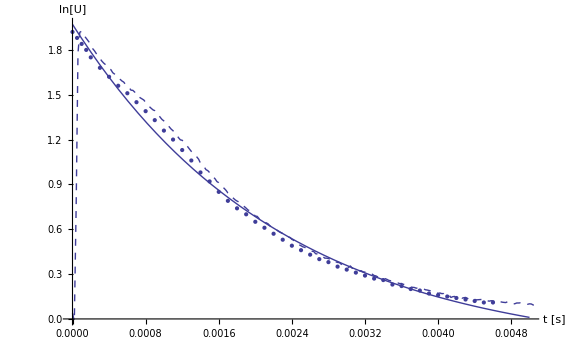

```mathematica
FID01MolLog=Replace[FID01Mol,{t_,U_}->{t,U},2];
Show[Plot[Normal[FitFID01Mol],{x,0,0.005}](*,Plot[Normal[FitFID01Mol2],{x,0,0.005},PlotStyle->{Green,Dashed}]*),ListLinePlot[FID01MolLog,PlotStyle->Dashed,PlotRange->Full],
ListPlot[FID01MolPeaks,ImageSize->Large],AxesLabel->{"t [s]","ln[U]"},ImageSize->Large]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 2.30827 | 0.0838511 | 27.5281 | 8.48259×10^-30
b | 0.0903278 | 0.00883108 | 10.2284 | 2.55107×10^-13
τ | 0.00291935 | 0.0000885437 | 32.9708 | 3.68529×10^-33
x0 | -0.00144061 | 0.000130686 | -11.0235 | 2.25145×10^-14

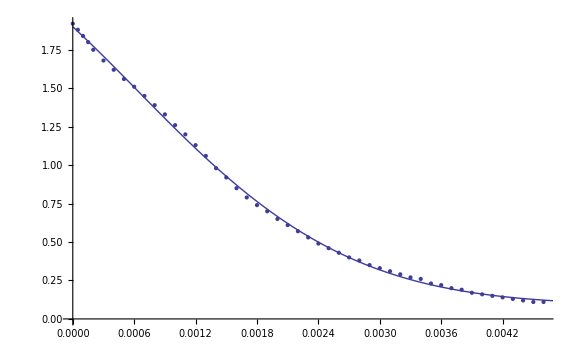

```mathematica
FitFID01Mol2=NonlinearModelFit[FID01MolPeaks,a*Exp[-((x-x0)/τ)^2]+b,{a,b,{τ,0.00013},{x0,0}},x,PrecisionGoal->4];
(* FitFID02Mol2=NonlinearModelFit[FID02MolPeaks,a*(x)^1.1+b,{a,b},x];*)
FitFID01Mol2["ParameterTable"]
(*FitFID02Mol2["ParameterTable"]*)
Show[ListPlot[FID01MolPeaks,ImageSize->Large],Plot[Normal[FitFID01Mol2],{x,0,0.005}](*,Plot[Normal[FitFID02Mol2],{x,0,0.005},PlotStyle->Green]*)]
```

### 0.2 Mol CuSO_4

```mathematica
ListLinePlot[FID02Mol,PlotRange->Full];
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 2.99657 | 0.0238501 | 125.641 | 2.87185×10^-81
b | -0.0761574 | 0.0216167 | -3.52309 | 0.000773492
τ | 0.00133728 | 0.0000315912 | 42.3309 | 4.45049×10^-50

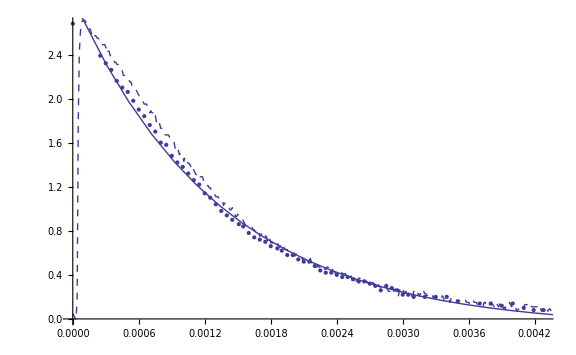

```mathematica
FitFID02Mol=NonlinearModelFit[FID02MolPeaks,a*Exp[-(x)/τ]+b,{a,b,τ},x,MaxIterations->Infinity];
(* FitFID02Mol2=NonlinearModelFit[FID02MolPeaks,a*(x)^1.1+b,{a,b},x];*)
FitFID02Mol["ParameterTable"]
(*FitFID02Mol2["ParameterTable"]*)
FID02MolLog=Replace[FID02Mol,{t_,U_}->{t,U},2];
Show[ListPlot[FID02MolPeaks,ImageSize->Large],Plot[Normal[FitFID02Mol],{x,-0.005,0.005}](*,Plot[Normal[FitFID02Mol2],{x,0,0.005},PlotStyle->Green]*),ListLinePlot[FID02MolLog,PlotStyle->Dashed]]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 4.59112 | 0.386961 | 11.8645 | 5.07111×10^-18
b | 0.116395 | 0.0102027 | 11.4083 | 2.92431×10^-17
τ | 0.00254112 | 0.000100819 | 25.2047 | 1.38657×10^-35
x0 | -0.00188733 | 0.00020359 | -9.27028 | 1.44357×10^-13

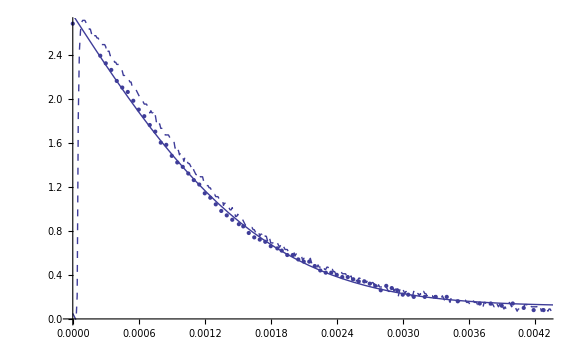

```mathematica
FitFID02Mol2=NonlinearModelFit[FID02MolPeaks,a*Exp[-((x-x0)/τ)^2]+b,{a,b,{τ,0.00013},{x0,0}},x,PrecisionGoal->4];
(* FitFID02Mol2=NonlinearModelFit[FID02MolPeaks,a*(x)^1.1+b,{a,b},x];*)
FitFID02Mol2["ParameterTable"]
(*FitFID02Mol2["ParameterTable"]*)
FID02MolLog=Replace[FID02Mol,{t_,U_}->{t,U},2];
Show[ListPlot[FID02MolPeaks,ImageSize->Large],Plot[Normal[FitFID02Mol2],{x,0,0.005}](*,Plot[Normal[FitFID02Mol2],{x,0,0.005},PlotStyle->Green]*),ListLinePlot[FID02MolLog,PlotStyle->Dashed]]
```

```mathematica
Plot[Normal[FitFID02Mol2],{x,-0.008,0.005}];
```

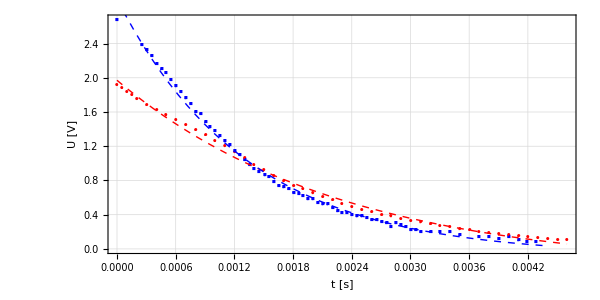

```mathematica
Show[ErrorListPlot[{CombineError[FID01MolPeaks,0.01],CombineError[FID02MolPeaks,0.01]},PlotMarkers->{Automatic,3},PlotStyle->{Red,Blue}],Plot[Normal[FitFID01Mol],{x,0,0.0046},PlotStyle->{Dashed,Red}],Plot[Normal[FitFID02Mol],{x,0,0.0044},PlotStyle->{Dashed,Blue}],niceStyle,FrameLabel->{"t [s]","U [V]"},AspectRatio->1.5/3]
```

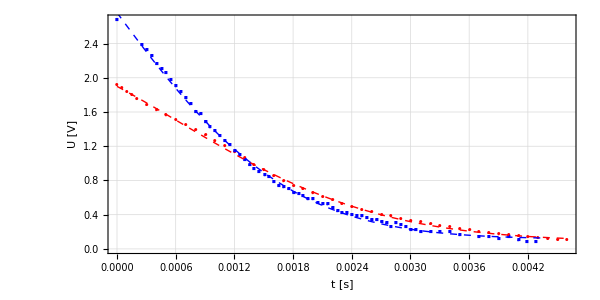

```mathematica
Show[ErrorListPlot[{CombineError[FID01MolPeaks,0.01],CombineError[FID02MolPeaks,0.01]},PlotMarkers->{Automatic,3},PlotStyle->{Red,Blue}],Plot[Normal[FitFID01Mol2],{x,0,0.0046},PlotStyle->{Dashed,Red}],Plot[Normal[FitFID02Mol2],{x,0,0.0044},PlotStyle->{Dashed,Blue}],niceStyle,FrameLabel->{"t [s]","U [V]"},AspectRatio->1.5/3]
```

#### Calculate Inhomogeneity

```mathematica
γ:=2.68* 10^8
```

```mathematica
DeltaGauss[t_]=(4 Sqrt[Log[2]])/(γ t);
DeltaLorentz[t_]=2/(γ t);
```

```mathematica
DeltaGauss[0.0025]
```

4.97935×10^-6

```mathematica
DeltaGauss[0.0025]*0.2/2.5
```

3.98348×10^-7

```mathematica
DeltaGauss[0.00229]
```

5.43597×10^-6

```mathematica
DeltaGauss[0.00229]*0.00009/0.00229
```

2.13641×10^-7

```mathematica
DeltaLorentz[2.3*10^-3]
```

3.24465×10^-6

```mathematica
DeltaLorentz[2.3*10^-3]*0.1/2.3
```

1.41072×10^-7

```mathematica
DeltaLorentz[1.34*10^-3]
```

5.56917×10^-6

```mathematica
DeltaLorentz[1.34*10^-3]*0.03/1.34
```

1.24683×10^-7

## Measurement of T2

### Spin Echo

```mathematica
FitModelFunction[V0_,T_,c_,t_]=V0*Exp[-(1000*2*t)/T]+c;
```

```mathematica
FitSE005Mol=NonlinearModelFit[SE005Mol,FitModelFunction[V0,τ,c,t],{V0,τ,c},t]
FitSE005Mol["ParameterTable"]
```

FittedModel[-0.146484+2.1166 ⅇ^(-105.101 t)]

| Estimate | Standard Error | t-Statistic | P-Value
V0 | 2.1166 | 0.0246131 | 85.995 | 3.03852×10^-28
τ | 19.0293 | 0.66575 | 28.5833 | 2.69086×10^-18
c | -0.146484 | 0.0275687 | -5.3134 | 0.0000287054

```mathematica
FitSE01Mol=NonlinearModelFit[SE01Mol,FitModelFunction[V0,τ,c,t],{V0,τ,c},t]
FitSE01Mol["ParameterTable"]
```

FittedModel[-0.0219455+1.92493 ⅇ^(-200.683 t)]

| Estimate | Standard Error | t-Statistic | P-Value
V0 | 1.92493 | 0.00666109 | 288.981 | 3.37598×10^-50
τ | 9.96595 | 0.104319 | 95.5337 | 9.38236×10^-37
c | -0.0219455 | 0.00628917 | -3.4894 | 0.00162051

```mathematica
FitSE02Mol=NonlinearModelFit[SE02Mol,FitModelFunction[V0,τ,c,t],{V0,τ,c},t]
FitSE02Mol["ParameterTable"]
```

FittedModel[0.0621387+2.73573 ⅇ^(-483.14 t)]

| Estimate | Standard Error | t-Statistic | P-Value
V0 | 2.73573 | 0.0104494 | 261.808 | 2.89889×10^-35
τ | 4.13959 | 0.0361257 | 114.588 | 1.8865×10^-28
c | 0.0621387 | 0.00496529 | 12.5146 | 1.27073×10^-10

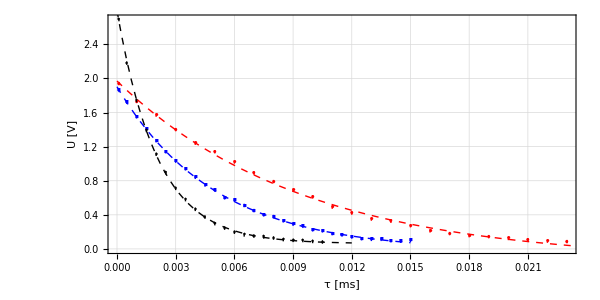

```mathematica
Show[ErrorListPlot[{CombineError[SE005Mol,0.02],CombineError[SE01Mol,0.02],CombineError[SE02Mol,0.02]},PlotMarkers->{Automatic,3},PlotStyle->{Red,Blue,Black}],
Plot[Normal[FitSE005Mol],{t,0,0.024},PlotStyle->{Red,Dashed}],
Plot[Normal[FitSE01Mol],{t,0,0.015},PlotStyle->{Blue,Dashed}],
Plot[Normal[FitSE02Mol],{t,0,0.012},PlotStyle->{Black,Dashed}],niceStyle,
FrameLabel->{"τ [ms]","U [V]"},BaseStyle->{FontFamily->"Arial",FontSize->16},ImageSize->600,AspectRatio->1.5/3]
```

### Carr - Purcell - Methode

```mathematica
FitModelFunctionCP[V0_,T_,t_,]=V0*Exp[-(10^3*t)/T];
```

FittedModel[0.162313+1.73733 ⅇ^(-99.4417 t) Cos[2.37404×10^-7 t]]

FittedModel[0.162313+1.73733 ⅇ^(-99.4417 t)]

| Estimate | Standard Error | t-Statistic | P-Value
V0 | 1.73733 | 0.0645207 | 26.9267 | 1.46848×10^-21
T | 10.0561 | 0.653798 | 15.3811 | 3.47954×10^-15
c | 0.162313 | 0.0422846 | 3.83858 | 0.000646692
δ | 1.08818×10^-8 | 1.26869×10^8 | 8.57715×10^-17 | 1

| Estimate | Standard Error | t-Statistic | P-Value
V0 | 1.73733 | 0.0303168 | 57.3058 | 2.1401×10^-31
T | 10.0561 | 0.432136 | 23.2708 | 2.608×10^-20
c | 0.162313 | 0.0177841 | 9.12682 | 5.02848×10^-10

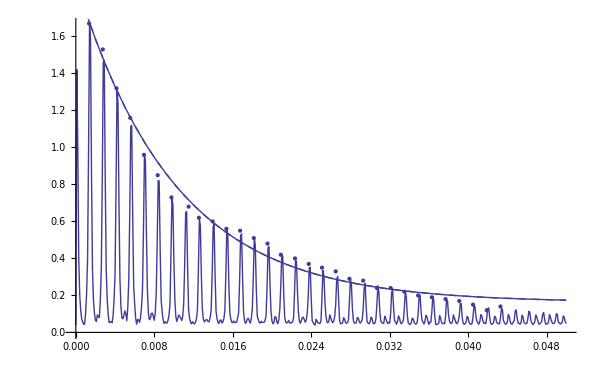

```mathematica
FitCP005Mol=NonlinearModelFit[CP005MolPeaks,V0*Exp[-(10^3*t)/T]*Cos[(δ*10^3*t)/(2*0.4)Degree]+c,{V0,{T,20},c,{δ,30}},t]
FitCP005Mol2=NonlinearModelFit[CP005MolPeaks,V0*Exp[-(10^3*t)/T]+c,{V0,T,c},t]
FitCP005Mol["ParameterTable"]
FitCP005Mol2["ParameterTable"]
Show[ListLinePlot[CP005Mol,PlotRange->Full],
ListPlot[CP005MolPeaks],Plot[Normal[FitCP005Mol2],{t,0,0.05},PlotStyle->{Dashed}],Plot[Normal[FitCP005Mol],{t,0,0.05}],ImageSize->600]
```

FittedModel[0.181323+1.73529 ⅇ^(-195.898 t) Cos[2.7631×10^-7 t]]

FittedModel[0.181323+1.73529 ⅇ^(-195.898 t)]

| Estimate | Standard Error | t-Statistic | P-Value
V0 | 1.73529 | 0.0569586 | 30.4658 | 2.74558×10^-21
T | 5.1047 | 0.299799 | 17.0271 | 2.89702×10^-15
c | 0.181323 | 0.0374893 | 4.83666 | 0.0000568945
δ | -1.26651×10^-8 | 3.79278×10^8 | -3.33927×10^-17 | 1

| Estimate | Standard Error | t-Statistic | P-Value
V0 | 1.73529 | 0.0273399 | 63.4708 | 4.81937×10^-30
T | 5.1047 | 0.19781 | 25.806 | 4.69545×10^-20
c | 0.181323 | 0.0160024 | 11.331 | 1.47843×10^-11

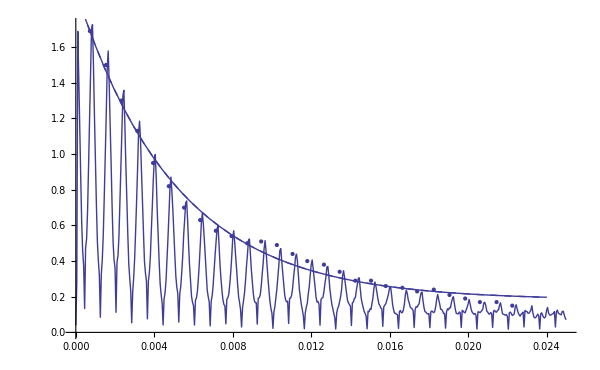

```mathematica
FitCP01Mol=NonlinearModelFit[CP01MolPeaks,V0*Exp[-(10^3*t)/T]*Cos[(δ*1000*t)/(2*0.4)Degree]+c,{V0,{T,10},c,{δ,20}},t]
FitCP01Mol2=NonlinearModelFit[CP01MolPeaks,V0*Exp[-(10^3*t)/T]+c,{V0,T,c},t]
FitCP01Mol["ParameterTable"]
FitCP01Mol2["ParameterTable"]
Show[ListLinePlot[CP01Mol,PlotRange->Full],
ListPlot[CP01MolPeaks],Plot[Normal[FitCP01Mol],{t,0,0.024}],Plot[Normal[FitCP01Mol2],{t,0,0.024},PlotStyle->Dashed],ImageSize->600]
```

FittedModel[0.428871+2.10383 ⅇ^(-231.153 t) Cos[254.545 t]]

FittedModel[-0.00305817+2.60668 ⅇ^(-268.72 t)]

| Estimate | Standard Error | t-Statistic | P-Value
V0 | 2.10383 | 0.0893331 | 23.5504 | 4.32058×10^-10
T | 4.32614 | 0.286687 | 15.0901 | 3.30062×10^-8
c | 0.428871 | 0.0642021 | 6.68002 | 0.0000549956
δ | 11.6675 | 1.13383 | 10.2904 | 1.22202×10^-6

| Estimate | Standard Error | t-Statistic | P-Value
V0 | 2.60668 | 0.0778625 | 33.478 | 2.01911×10^-12
T | 3.72135 | 0.322401 | 11.5426 | 1.73266×10^-7
c | -0.00305817 | 0.0778866 | -0.0392644 | 0.969383

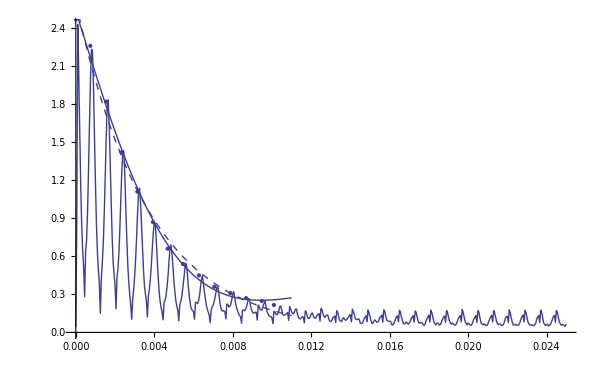

```mathematica
FitCP02Mol=NonlinearModelFit[CP02MolPeaks,V0*Exp[-(10^3*t)/T]*Cos[(δ*1000*t)/(2*0.4)Degree]+c,{V0,T,{c,0.04},{δ,5.}},t]
FitCP02Mol2=NonlinearModelFit[CP02MolPeaks,V0*Exp[-(10^3*t)/T]+c,{V0,T,{c,0.04}},t]
FitCP02Mol["ParameterTable"]
FitCP02Mol2["ParameterTable"]
Show[ListLinePlot[CP02Mol,PlotRange->Full],
ListPlot[CP02MolPeaks],Plot[Normal[FitCP02Mol],{t,0,0.011}],Plot[Normal[FitCP02Mol2],{t,0,0.011},PlotStyle->Dashed],ImageSize->600]
```

```mathematica
ListPlot[{CP02Mol90degPeaks,CP02MolPeaks},PlotMarkers->{"π/2","3/2π"}];
```

FittedModel[0.644093+1.87805 ⅇ^(-190.514 t) Cos[398.589 t]]

FittedModel[-0.789667+3.40464 ⅇ^(-205.727 t)]

| Estimate | Standard Error | t-Statistic | P-Value
V0 | 1.87805 | 0.13587 | 13.8224 | 0.0000355909
T | 5.24897 | 0.61862 | 8.48496 | 0.000373681
c | 0.644093 | 0.108937 | 5.91252 | 0.00197135
δ | -18.27 | 1.61023 | -11.3462 | 0.000093018

| Estimate | Standard Error | t-Statistic | P-Value
V0 | 3.40464 | 0.4135 | 8.23372 | 0.000173358
T | 4.86082 | 1.16829 | 4.16061 | 0.00594034
c | -0.789667 | 0.45031 | -1.75361 | 0.13004

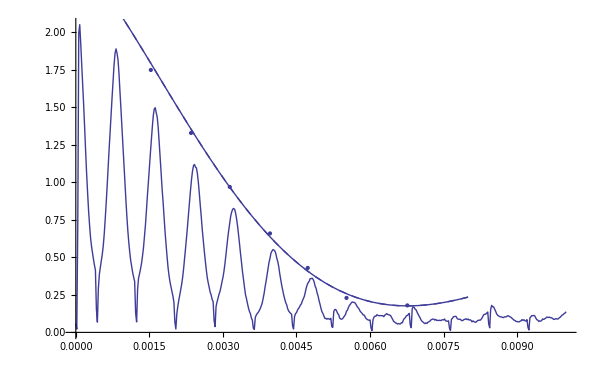

```mathematica
FitCP02Mol90deg=NonlinearModelFit[CP02Mol90degPeaks,V0*Exp[-(10^3*t)/T]*Cos[(δ*1000*t)/(2*0.4)Degree]+c,{V0,T,{c,0.04},{δ,5.}},t]
FitCP02Mol90deg2=NonlinearModelFit[CP02Mol90degPeaks,V0*Exp[-(10^3*t)/T]+c,{V0,T,{c,0.04}},t]
FitCP02Mol90deg["ParameterTable"]
FitCP02Mol90deg2["ParameterTable"]
Show[ListLinePlot[CP02Mol90deg,PlotRange->Full],
ListPlot[CP02Mol90degPeaks,PlotRange->Full],Plot[Normal[FitCP02Mol90deg],{t,0,0.008},PlotRange->Full],Plot[Normal[FitCP02Mol90deg],{t,0,0.008},PlotStyle->Dashed],ImageSize->600]
```

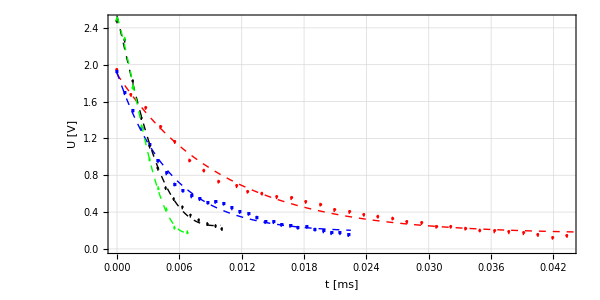

```mathematica
Show[
ErrorListPlot[{CombineError[CP005MolPeaks,0.02],CombineError[CP01MolPeaks,0.02],CombineError[CP02MolPeaks,0.02],CombineError[CP02Mol90degPeaks,0.02]},PlotMarkers->{Automatic,2},PlotStyle->{Red,Blue,Black,Green}],
Plot[Abs[Normal[FitCP005Mol]],{t,0,0.045},PlotStyle->{Red,Dashed}],
Plot[Abs[Normal[FitCP01Mol]],{t,0,0.0225},PlotStyle->{Blue,Dashed}],
Plot[Abs[Normal[FitCP02Mol]],{t,0,0.01},PlotStyle->{Black,Dashed}],
Plot[Abs[Normal[FitCP02Mol90deg]],{t,0,0.007},PlotStyle->{Green,Dashed}],
niceStyle,FrameLabel->{"t [ms]","U [V]"},BaseStyle->{FontFamily->"Arial",FontSize->16},ImageSize->600,AspectRatio->1.5/3]
```

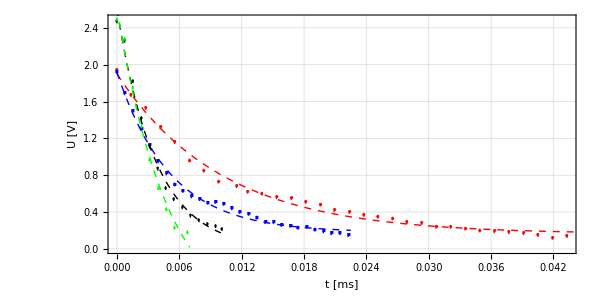

```mathematica
Show[
ErrorListPlot[{CombineError[CP005MolPeaks,0.02],CombineError[CP01MolPeaks,0.02],CombineError[CP02MolPeaks,0.02],CombineError[CP02Mol90degPeaks,0.02]},PlotMarkers->{Automatic,2},PlotStyle->{Red,Blue,Black,Green}],
Plot[Abs[Normal[FitCP005Mol2]],{t,0,0.045},PlotStyle->{Red,Dashed}],
Plot[Abs[Normal[FitCP01Mol2]],{t,0,0.0225},PlotStyle->{Blue,Dashed}],
Plot[Abs[Normal[FitCP02Mol2]],{t,0,0.01},PlotStyle->{Black,Dashed}],
Plot[Abs[Normal[FitCP02Mol90deg2]],{t,0,0.007},PlotStyle->{Green,Dashed}],
niceStyle,FrameLabel->{"t [ms]","U [V]"},BaseStyle->{FontFamily->"Arial",FontSize->16},ImageSize->600,AspectRatio->1.5/3]
```

### Meiboom - Gill - Methode

```mathematica
FitModelFunctionMG[V0_,T_,c_,t_,]=V0*Exp[-(10^3*t)/T]+c;
```

FittedModel[0.103959+1.81746 ⅇ^(-72.4394 t)]

FittedModel[0.123179+1.75927 ⅇ^(-73.6405 t)]

| Estimate | Standard Error | t-Statistic | P-Value
V0 | 1.81746 | 0.0259646 | 69.9975 | 2.76525×10^-20
T | 13.8046 | 0.547367 | 25.2201 | 1.07073×10^-13
c | 0.103959 | 0.0208081 | 4.99609 | 0.000159575

| Estimate | Standard Error | t-Statistic | P-Value
V0 | 1.75927 | 0.0380428 | 46.2445 | 1.34902×10^-17
T | 13.5795 | 0.799286 | 16.9895 | 3.30598×10^-11
c | 0.123179 | 0.0267384 | 4.6068 | 0.000342334

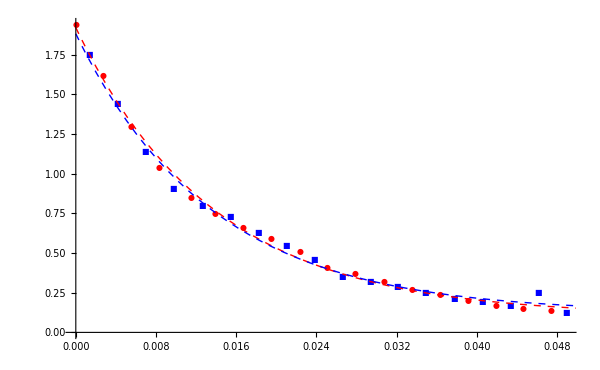

```mathematica
FitMG005Mol=NonlinearModelFit[MG005MolPeaks[[;;;;2]],V0*Exp[-(10^3*t)/T]+c,{V0,{T,20},c},t]
FitMG005Mol2=NonlinearModelFit[MG005MolPeaks[[2;;;;2]],V0*Exp[-(10^3*t)/T]+c,{V0,{T,20},c},t]
FitMG005Mol["ParameterTable"]
FitMG005Mol2["ParameterTable"]
Show[ListPlot[{MG005MolPeaks[[;;;;2]],MG005MolPeaks[[2;;;;2]]},PlotMarkers->{Automatic,8},PlotStyle->{Red,Blue}],Plot[Normal[FitMG005Mol],{t,0,0.05},PlotStyle->{Dashed,Red}],Plot[Normal[FitMG005Mol2],{t,0,0.05},PlotStyle->{Dashed,Blue}],ImageSize->600]
```

FittedModel[0.160031+1.74024 ⅇ^(-156.91 t)]

FittedModel[0.139122+1.68135 ⅇ^(-147.158 t)]

| Estimate | Standard Error | t-Statistic | P-Value
V0 | 1.74024 | 0.0290298 | 59.9469 | 3.06997×10^-16
T | 6.37309 | 0.292474 | 21.7903 | 5.11495×10^-11
c | 0.160031 | 0.0229955 | 6.95926 | 0.0000151874

| Estimate | Standard Error | t-Statistic | P-Value
V0 | 1.68135 | 0.0361227 | 46.5455 | 5.51093×10^-14
T | 6.79541 | 0.434277 | 15.6476 | 7.29779×10^-9
c | 0.139122 | 0.0308462 | 4.51017 | 0.000886252

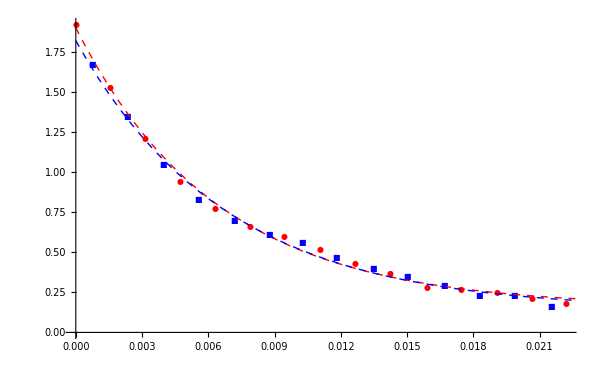

```mathematica
FitMG01Mol=NonlinearModelFit[MG01MolPeaks[[;;;;2]],V0*Exp[-(10^3*t)/T]+c,{V0,T,c},t]
FitMG01Mol2=NonlinearModelFit[MG01MolPeaks[[2;;;;2]],V0*Exp[-(10^3*t)/T]+c,{V0,T,c},t]
FitMG01Mol["ParameterTable"]
FitMG01Mol2["ParameterTable"]
Show[ListPlot[{MG01MolPeaks[[;;;;2]],MG01MolPeaks[[2;;;;2]]},PlotMarkers->{Automatic,8},PlotStyle->{Red,Blue}],Plot[Normal[FitMG01Mol],{t,0,0.025},PlotStyle->{Dashed,Red}],Plot[Normal[FitMG01Mol2],{t,0,0.025},PlotStyle->{Dashed,Blue}],ImageSize->600]
```

FittedModel[-0.0811076+2.60408 ⅇ^(-200.68 t)]

FittedModel[0.0406994+2.7062 ⅇ^(-248.524 t)]

| Estimate | Standard Error | t-Statistic | P-Value
V0 | 2.60408 | 0.0649877 | 40.0704 | 1.61477×10^-8
T | 4.98306 | 0.342792 | 14.5367 | 6.64626×10^-6
c | -0.0811076 | 0.0665009 | -1.21965 | 0.268363

| Estimate | Standard Error | t-Statistic | P-Value
V0 | 2.7062 | 0.0298707 | 90.5972 | 3.10572×10^-9
T | 4.02375 | 0.141735 | 28.3893 | 1.01571×10^-6
c | 0.0406994 | 0.0277902 | 1.46452 | 0.202935

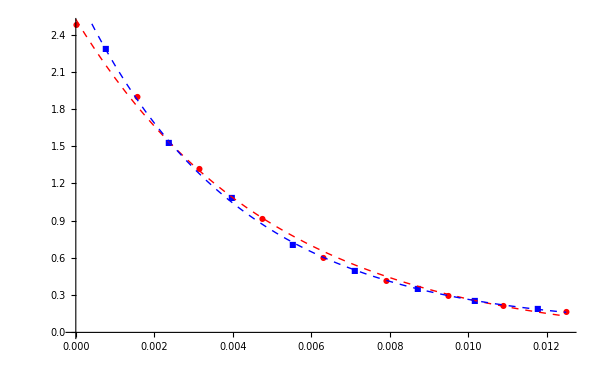

```mathematica
FitMG02Mol90deg=NonlinearModelFit[MG02Mol90degPeaks[[;;;;2]],V0*Exp[-(10^3*t)/T]+c,{V0,T,c},t]
FitMG02Mol90deg2=NonlinearModelFit[MG02Mol90degPeaks[[2;;;;2]],V0*Exp[-(10^3*t)/T]+c,{V0,T,c},t]
FitMG02Mol90deg["ParameterTable"]
FitMG02Mol90deg2["ParameterTable"]
Show[ListPlot[{MG02Mol90degPeaks[[;;;;2]],MG02Mol90degPeaks[[2;;;;2]]},PlotMarkers->{Automatic,8},PlotStyle->{Red,Blue}],Plot[Normal[FitMG02Mol90deg],{t,0,0.0125},PlotStyle->{Dashed,Red}],Plot[Normal[FitMG02Mol90deg2],{t,0,0.0125},PlotStyle->{Dashed,Blue}],ImageSize->600]
```

FittedModel[0.00023135+2.54296 ⅇ^(-242.448 t)]

FittedModel[0.086648+2.71349 ⅇ^(-290.161 t)]

| Estimate | Standard Error | t-Statistic | P-Value
V0 | 2.54296 | 0.0832818 | 30.5344 | 7.06932×10^-7
T | 4.1246 | 0.369953 | 11.149 | 0.000101252
c | 0.00023135 | 0.0817981 | 0.0028283 | 0.997853

| Estimate | Standard Error | t-Statistic | P-Value
V0 | 2.71349 | 0.0201286 | 134.808 | 1.81605×10^-8
T | 3.44636 | 0.082234 | 41.9092 | 1.93762×10^-6
c | 0.086648 | 0.0184238 | 4.70304 | 0.00928744

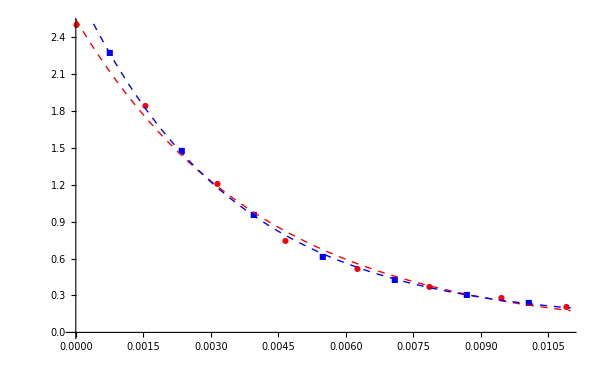

```mathematica
FitMG02Mol=NonlinearModelFit[MG02MolPeaks[[;;;;2]],V0*Exp[-(10^3*t)/T]+c,{V0,T,c},t]
FitMG02Mol2=NonlinearModelFit[MG02MolPeaks[[2;;;;2]],V0*Exp[-(10^3*t)/T]+c,{V0,T,c},t]
FitMG02Mol["ParameterTable"]
FitMG02Mol2["ParameterTable"]
Show[ListPlot[{MG02MolPeaks[[;;;;2]],MG02MolPeaks[[2;;;;2]]},PlotMarkers->{Automatic,8},PlotStyle->{Red,Blue}],Plot[Normal[FitMG02Mol],{t,0,0.011},PlotStyle->{Dashed,Red}],Plot[Normal[FitMG02Mol2],{t,0,0.011},PlotStyle->{Dashed,Blue}],ImageSize->600]
```

```mathematica
{{"", "Estimate", "Standard Error", "t-Statistic", "P-Value"}, {V0, 2.5429612359703175, 0.08328178483557967, 30.534422875191705, 7.069316369159749*^-7}, {T, 4.1245990801294115, 0.3699529198297211, 11.148983719409076, 0.00010125181383060914}, {c, 0.00023135000961237067, 0.08179813856007609, 0.002828304087170116, 0.9978527171306824}}s
```

s  | Estimate | Standard Error | t-Statistic | P-Value
V0 | 2.54296 | 0.0832818 | 30.5344 | 7.06932×10^-7
T | 4.1246 | 0.369953 | 11.149 | 0.000101252
c | 0.00023135 | 0.0817981 | 0.0028283 | 0.997853

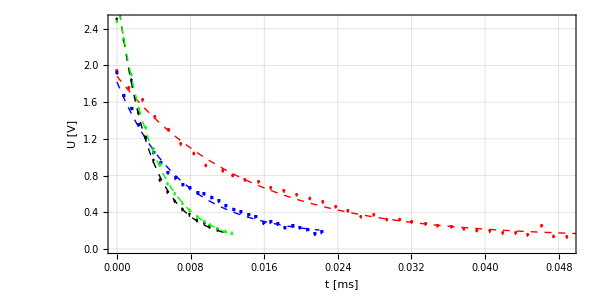

```mathematica
Show[
ErrorListPlot[{CombineError[MG005MolPeaks,0.02],CombineError[MG01MolPeaks,0.02],CombineError[MG02MolPeaks,0.02],CombineError[MG02Mol90degPeaks,0.02]},PlotMarkers->{Automatic,2},PlotStyle->{Red,Blue,Black,Green}],
Plot[Abs[Normal[FitMG005Mol2]],{t,0,0.05},PlotStyle->{Red,Dashed}],
Plot[Abs[Normal[FitMG01Mol2]],{t,0,0.022},PlotStyle->{Blue,Dashed}],
Plot[Abs[Normal[FitMG02Mol2]],{t,0,0.012},PlotStyle->{Black,Dashed}],
Plot[Abs[Normal[FitMG02Mol90deg2]],{t,0,0.012},PlotStyle->{Green,Dashed}],
niceStyle,FrameLabel->{"t [ms]","U [V]"},BaseStyle->{FontFamily->"Arial",FontSize->16},ImageSize->600,AspectRatio->1.5/3]
```

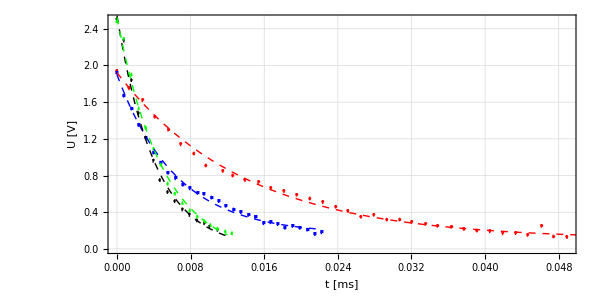

```mathematica
Show[
ErrorListPlot[{CombineError[MG005MolPeaks,0.02],CombineError[MG01MolPeaks,0.02],CombineError[MG02MolPeaks,0.02],CombineError[MG02Mol90degPeaks,0.02]},PlotMarkers->{Automatic,2},PlotStyle->{Red,Blue,Black,Green}],
Plot[Abs[Normal[FitMG005Mol]],{t,0,0.05},PlotStyle->{Red,Dashed}],
Plot[Abs[Normal[FitMG01Mol]],{t,0,0.022},PlotStyle->{Blue,Dashed}],
Plot[Abs[Normal[FitMG02Mol]],{t,0,0.012},PlotStyle->{Black,Dashed}],
Plot[Abs[Normal[FitMG02Mol90deg]],{t,0,0.012},PlotStyle->{Green,Dashed}],
niceStyle,FrameLabel->{"t [ms]","U [V]"},BaseStyle->{FontFamily->"Arial",FontSize->16},ImageSize->600,AspectRatio->1.5/3]
```

## Measurement of T1

### Determination of T_1

```mathematica
FitModelFunctionIR[V0_,T_,t_]=V0(1-2*Exp[-(1000*t)/T]);
```

```mathematica
FitIR005Mol=NonlinearModelFit[IR005Mol,FitModelFunctionIR[V0,τ,t],{V0,τ},t];
FitIR005Mol["ParameterTable"]
IR005MolPlot=Replace[IR005Mol,{t_,V_}->{t,Abs[V]},2];
Show[ListPlot[IR005MolPlot],Plot[Abs[Normal[FitIR005Mol]],{t,0,0.11}]];
```

| Estimate | Standard Error | t-Statistic | P-Value
V0 | 1.8743 | 0.0120815 | 155.138 | 6.81652×10^-44
τ | 20.6663 | 0.157339 | 131.348 | 8.45689×10^-42

```mathematica
FitIR01Mol=NonlinearModelFit[IR01Mol,FitModelFunctionIR[V0,τ,t],{V0,τ},t];
FitIR01Mol["ParameterTable"]
IR01MolPlot=Replace[IR01Mol,{t_,V_}->{t,Abs[V]},2];
Show[ListPlot[IR01MolPlot],Plot[Abs[Normal[FitIR01Mol]],{t,0,0.05}]];
```

| Estimate | Standard Error | t-Statistic | P-Value
V0 | 1.87655 | 0.0110441 | 169.914 | 1.22855×10^-63
τ | 10.2291 | 0.0601159 | 170.156 | 1.15397×10^-63

```mathematica
FitIR02Mol=NonlinearModelFit[IR02Mol,FitModelFunctionIR[V0,τ,t],{V0,τ},t];
FitIR02Mol["ParameterTable"]
IR02MolPlot=Replace[IR02Mol,{t_,V_}->{t,Abs[V]},2];
Show[ListPlot[IR02MolPlot],Plot[Abs[Normal[FitIR02Mol]],{t,0,0.02}]];
```

| Estimate | Standard Error | t-Statistic | P-Value
V0 | 2.66223 | 0.0124765 | 213.38 | 2.12709×10^-53
τ | 4.46701 | 0.0299937 | 148.932 | 2.99191×10^-48

```mathematica
FitIR02Mol90deg=NonlinearModelFit[IR02Mol90deg,FitModelFunctionIR[V0,τ,t],{V0,τ},t];
FitIR02Mol90deg["ParameterTable"]
IR02Mol90degPlot=Replace[IR02Mol,{t_,V_}->{t,Abs[V]},2];
Show[ListPlot[IR02Mol90degPlot],Plot[Abs[Normal[FitIR02Mol90deg]],{t,0,0.02}]];
```

| Estimate | Standard Error | t-Statistic | P-Value
V0 | 2.69308 | 0.0114676 | 234.842 | 9.01846×10^-55
τ | 4.41481 | 0.0271971 | 162.327 | 1.75107×10^-49

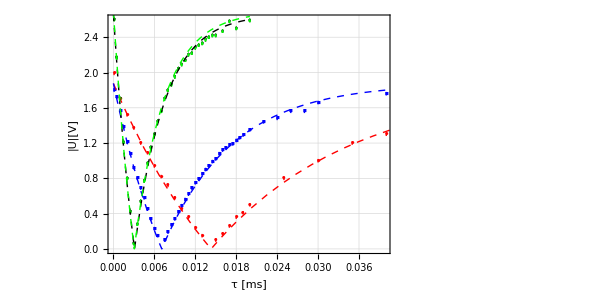

```mathematica
Show[ErrorListPlot[{CombineError[IR005MolPlot,0.02],CombineError[IR01MolPlot,0.02],CombineError[IR02MolPlot,0.02],CombineError[IR02Mol90degPlot,0.02]},PlotMarkers->{Automatic,2},PlotStyle->{Red,Blue,Black,Green}],
Plot[Abs[Normal[FitIR005Mol]],{t,0,0.11},PlotStyle->{Red,Dashed}],
Plot[Abs[Normal[FitIR01Mol]],{t,0,0.05},PlotStyle->{Blue,Dashed}],
Plot[Abs[Normal[FitIR02Mol]],{t,0,0.02},PlotStyle->{Black,Dashed}],
Plot[Abs[Normal[FitIR02Mol90deg]],{t,0,0.02},PlotStyle->{Green,Dashed}],
FrameLabel->{"τ [ms]","|U|[V]"},BaseStyle->{FontFamily->"Arial",FontSize->16},ImageSize->600,AspectRatio->1.5/3,niceStyle]
```

## Influence of Concentration of CuSO_4 on Relaxation Times

### Influence on T_1

FittedModel[-0.872615+1.08169 x]

| Estimate | Standard Error | t-Statistic | P-Value
1 | -0.872615 | 0.224031 | -3.89506 | 0.0600384
x | 1.08169 | 0.0191055 | 56.6169 | 0.000311821

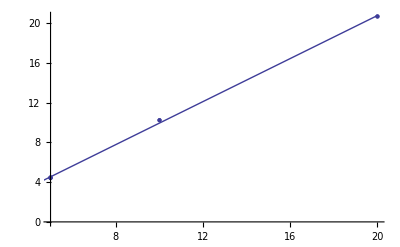

```mathematica
IRDataTempErr={{0.05,FitIR005Mol["ParameterTable"][[1,1,3,2]],FitIR005Mol["ParameterTable"][[1,1,3,3]]},
{0.1,FitIR01Mol["ParameterTable"][[1,1,3,2]],FitIR01Mol["ParameterTable"][[1,1,3,3]]},
{0.2,FitIR02Mol["ParameterTable"][[1,1,3,2]],FitIR02Mol["ParameterTable"][[1,1,3,3]]},
{0.2,FitIR02Mol90deg["ParameterTable"][[1,1,3,2]],FitIR02Mol90deg["ParameterTable"][[1,1,3,3]]}};
IRDataTemp={{0.05,FitIR005Mol["ParameterTable"][[1,1,3,2]]},
{0.1,FitIR01Mol["ParameterTable"][[1,1,3,2]]},
{0.2,FitIR02Mol["ParameterTable"][[1,1,3,2]]},
{0.2,FitIR02Mol90deg["ParameterTable"][[1,1,3,2]]}};
IRData=Replace[IRDataTemp,{n_,T_}->{n^-1,T},2];
IRDataErr=Replace[IRDataTempErr,{n_,T_,De_}->{n^-1,T,De},2];
FitIR=LinearModelFit[IRData,x,x]
LinearModelFit[IRData,x,x]["ParameterTable"]
Show[ErrorListPlot[IRDataErr],ListPlot[IRData],Plot[Normal[FitIR],{x,0,20},PlotRange->All]]
```

### Influence on T_2

#### Spin Echo

{{0.05,19.0293},{0.1,9.96595},{0.2,4.13959}}

FittedModel[-0.392112+0.980321 x]

| Estimate | Standard Error | t-Statistic | P-Value
1 | -0.392112 | 0.847558 | -0.462637 | 0.724144
x | 0.980321 | 0.0640693 | 15.3009 | 0.0415475

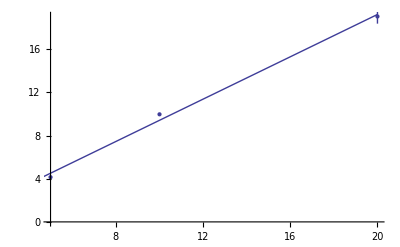

```mathematica
SEDataTempErr={{0.05,FitSE005Mol["ParameterTable"][[1,1,3,2]],FitSE005Mol["ParameterTable"][[1,1,3,3]]},
{0.1,FitSE01Mol["ParameterTable"][[1,1,3,2]],FitSE01Mol["ParameterTable"][[1,1,3,3]]},
{0.2,FitSE02Mol["ParameterTable"][[1,1,3,2]],FitSE02Mol["ParameterTable"][[1,1,3,3]]}};
SEDataTemp={{0.05,FitSE005Mol["ParameterTable"][[1,1,3,2]]},
{0.1,FitSE01Mol["ParameterTable"][[1,1,3,2]]},
{0.2,FitSE02Mol["ParameterTable"][[1,1,3,2]]}}
SEData=Replace[SEDataTemp,{n_,T_}->{n^-1,T},2];
SEDataErr=Replace[SEDataTempErr,{n_,T_,De_}->{n^-1,T,De},2];
FitSE=LinearModelFit[SEData,x,x]
LinearModelFit[SEData,x,x]["ParameterTable"]
Show[ErrorListPlot[SEDataErr],ListPlot[SEDataErr],Plot[Normal[FitSE],{x,0,20},PlotRange->All]]
```

#### CP

FittedModel[1.24562+0.432724 x]

| Estimate | Standard Error | t-Statistic | P-Value
1 | 1.24562 | 0.715127 | 1.74182 | 0.331785
x | 0.432724 | 0.0540585 | 8.00472 | 0.0791206

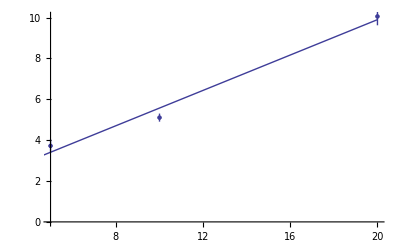

```mathematica
CPDataTemp={{0.05,FitCP005Mol2["ParameterTable"][[1,1,3,2]]},
{0.1,FitCP01Mol2["ParameterTable"][[1,1,3,2]]},
{0.2,FitCP02Mol2["ParameterTable"][[1,1,3,2]]}};
CPDataTempErr={{0.05,FitCP005Mol2["ParameterTable"][[1,1,3,2]],FitCP005Mol2["ParameterTable"][[1,1,3,3]]},
{0.1,FitCP01Mol2["ParameterTable"][[1,1,3,2]],FitCP01Mol2["ParameterTable"][[1,1,3,3]]},
{0.2,FitCP02Mol2["ParameterTable"][[1,1,3,2]],FitCP02Mol2["ParameterTable"][[1,1,3,3]]}};
CPData=Replace[CPDataTemp,{n_,T_}->{n^-1,T},2];
CPDataErr=Replace[CPDataTempErr,{n_,T_,De_}->{n^-1,T,De},2];
FitCP=LinearModelFit[CPData,x,x]
LinearModelFit[CPData,x,x]["ParameterTable"]
Show[ErrorListPlot[CPDataErr],ListPlot[CPData],Plot[Normal[FitCP],{x,0,20},PlotRange->All]]
```

#### MG

{{20.,13.5795},{10.,6.79541},{5.,3.44636}}

{{20.,13.8046,0.547367},{10.,6.37309,0.292474},{5.,4.1246,0.369953}}

FittedModel[0.408825+0.65931 x]

FittedModel[0.0543212+0.675951 x]

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.408825 | 0.96056 | 0.425611 | 0.743832
x | 0.65931 | 0.0726115 | 9.07997 | 0.0698311

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.0543212 | 0.0281414 | 1.9303 | 0.304296
x | 0.675951 | 0.00212729 | 317.753 | 0.0020035

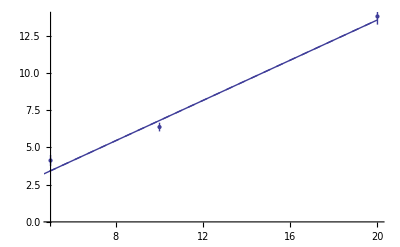

```mathematica
MGDataTemp={{0.05,FitMG005Mol["ParameterTable"][[1,1,3,2]]},
{0.1,FitMG01Mol["ParameterTable"][[1,1,3,2]]},
{0.2,FitMG02Mol["ParameterTable"][[1,1,3,2]]}};
MGData=Replace[MGDataTemp,{n_,T_}->{n^-1,T},2];
MGDataTempErr={{0.05,FitMG005Mol["ParameterTable"][[1,1,3,2]],FitMG005Mol["ParameterTable"][[1,1,3,3]]},
{0.1,FitMG01Mol["ParameterTable"][[1,1,3,2]],FitMG01Mol["ParameterTable"][[1,1,3,3]]},
{0.2,FitMG02Mol["ParameterTable"][[1,1,3,2]],FitMG02Mol["ParameterTable"][[1,1,3,3]]}};
MGDataTemp2={{0.05,FitMG005Mol2["ParameterTable"][[1,1,3,2]]},
{0.1,FitMG01Mol2["ParameterTable"][[1,1,3,2]]},
{0.2,FitMG02Mol2["ParameterTable"][[1,1,3,2]]}};
MGData2=Replace[MGDataTemp2,{n_,T_}->{n^-1,T},2]
MGDataTempErr2={{0.05,FitMG005Mol2["ParameterTable"][[1,1,3,2]],FitMG005Mol2["ParameterTable"][[1,1,3,3]]},
{0.1,FitMG01Mol2["ParameterTable"][[1,1,3,2]],FitMG01Mol2["ParameterTable"][[1,1,3,3]]},
{0.2,FitMG02Mol2["ParameterTable"][[1,1,3,2]],FitMG02Mol2["ParameterTable"][[1,1,3,3]]}};
MGDataErr2=Replace[MGDataTempErr,{n_,T_,De_}->{n^-1,T,De},2]
FitMG=LinearModelFit[MGData,x,x]
FitMG2=LinearModelFit[MGData2,x,x]
FitMG["ParameterTable"]
FitMG2["ParameterTable"]
Show[ErrorListPlot[MGDataErr2],Plot[Normal[FitMG2],{x,0,20},PlotStyle->Dashed],Plot[Normal[FitMG2],{x,0,20},PlotRange->All]]
```

### All in All

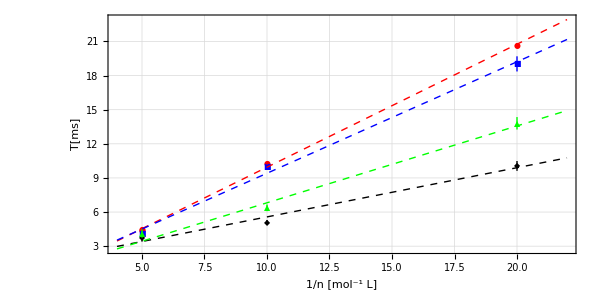

```mathematica
Show[ErrorListPlot[{IRDataErr,SEDataErr,CPDataErr,MGDataErr2},PlotMarkers->{Automatic,8},PlotStyle->{Red,Blue,Black,Green}],
Plot[Normal[FitIR],{x,4,22},PlotStyle->{Red,Dashed}],
Plot[Normal[FitSE],{x,4,22},PlotStyle->{Blue,Dashed}],
Plot[Normal[FitCP],{x,4,22},PlotStyle->{Black,Dashed}],
Plot[Normal[FitMG2],{x,4,22},PlotStyle->{Green,Dashed}],
FrameLabel->{"1/n [mol^-1 L]","T[ms]"},niceStyle,ImageSize->600,AspectRatio->1.5/3,PlotRange->All,AxesOrigin->{4,0}]
```

```mathematica
litvalT1=ReadList["litval_t1.txt",{Real,Real,Real}];
LitValT1Data=Replace[litvalT1,{n_,T_,De_}->{(10^-3 n)^-1,10^-3 T,10^-3 De},2]
Drop[LitValT1Data,None,2];
LitValT1=LinearModelFit[Drop[LitValT1Data,None,-1],x,x]
LitValT1["ParameterTable"]
```

{{10000.,2.501,0.024},{1000.,0.96,0.016},{333.333,0.439,0.005},{100.,0.163,0.002},{33.3333,0.0557,0.0004},{10.,0.0152,0.002}}

FittedModel[0.248602+0.000230231 x]

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.248602 | 0.137359 | 1.80988 | 0.144568
x | 0.000230231 | 0.0000334586 | 6.88107 | 0.00233736

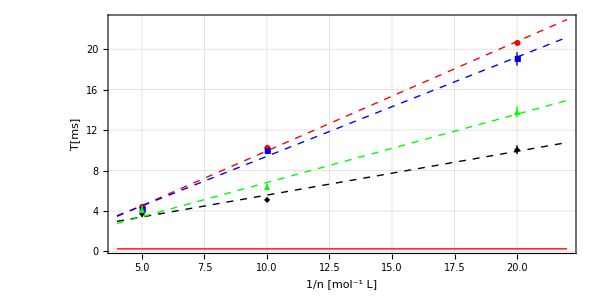

```mathematica
Show[ErrorListPlot[{IRDataErr,SEDataErr,CPDataErr,MGDataErr2},PlotMarkers->{Automatic,8},PlotStyle->{Red,Blue,Black,Green,Red}],
Plot[Normal[FitIR],{x,4,22},PlotStyle->{Red,Dashed}],
Plot[Normal[FitSE],{x,4,22},PlotStyle->{Blue,Dashed}],
Plot[Normal[FitCP],{x,4,22},PlotStyle->{Black,Dashed}],
Plot[Normal[FitMG2],{x,4,22},PlotStyle->{Green,Dashed}],
Plot[Normal[LitValT1],{x,4,22},PlotStyle->{Red}],
FrameLabel->{"1/n [mol^-1 L]","T[ms]"},niceStyle,ImageSize->600,AspectRatio->1.5/3,PlotRange->All,AxesOrigin->{4,0}]
```

FittedModel[-0.0347815+2.63347 ⅇ^(-261.97 t)]

| Estimate | Standard Error | t-Statistic | P-Value
V0 | 2.63347 | 0.0909766 | 28.9467 | 5.64285×10^-11
T | 3.81724 | 0.374977 | 10.1799 | 1.34954×10^-6
c | -0.0347815 | 0.0964409 | -0.360651 | 0.725862

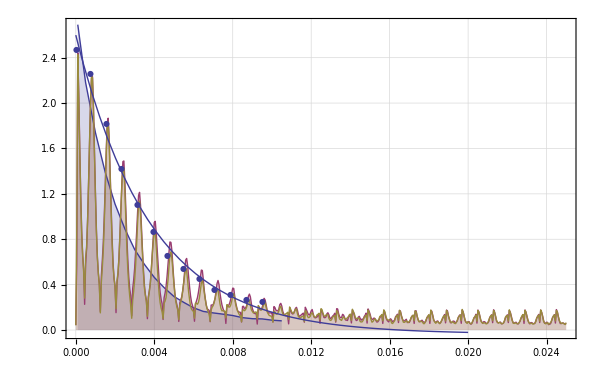

```mathematica
Test1=NonlinearModelFit[Drop[CP02MolPeaks,-1],V0*Exp[-(10^3*(t))/T]+c,{V0,T,{c,0.1}},t]
Test1["ParameterTable"]
Show[ListLinePlot[{SE02Mol,MG02Mol,CP02Mol},Filling->Axis,PlotRange->All],Plot[Normal[Test1],{t,0,0.02},PlotStyle->{Thick}],ListPlot[Drop[CP02MolPeaks,-1],PlotMarkers->{Automatic,8}],niceStyle]
```

FittedModel[0.162313+1.73733 ⅇ^(-99.4417 t)]

| Estimate | Standard Error | t-Statistic | P-Value
V0 | 1.73733 | 0.0303168 | 57.3058 | 2.1401×10^-31
T | 10.0561 | 0.432136 | 23.2708 | 2.608×10^-20
c | 0.162313 | 0.0177841 | 9.12682 | 5.02848×10^-10

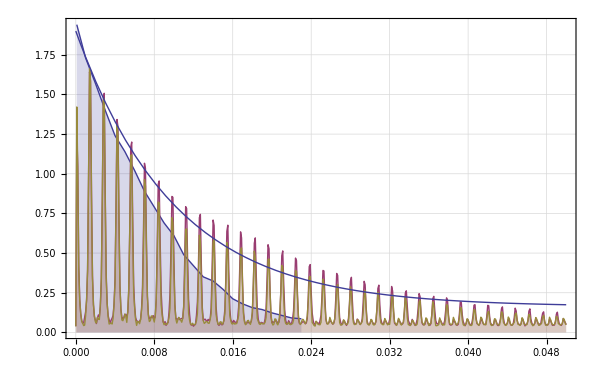

```mathematica
Test2=NonlinearModelFit[Drop[CP005MolPeaks,None],V0*Exp[-(10^3*(t))/T]+c,{V0,T,{c,0.1}},t]
Test2["ParameterTable"]
Show[ListLinePlot[{SE005Mol,MG005Mol,CP005Mol},Filling->Axis,PlotRange->All],Plot[Normal[Test2],{t,0,0.05},PlotStyle->{Thick}],niceStyle]
```

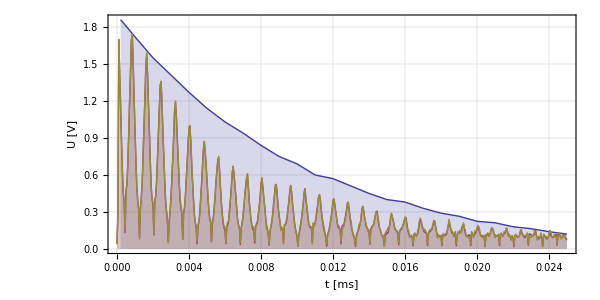

```mathematica
PlotSe=Drop[Replace[SE01Mol,{t_,V_}->{2*t,V},2],-5];
Show[ListLinePlot[{PlotSe,CP01Mol,MG01Mol},PlotRange->All,Filling->Axis,PlotRange->{0,0.25}],niceStyle,AspectRatio->1.5/3,FrameLabel->{"t [ms]","U [V]"}]
```

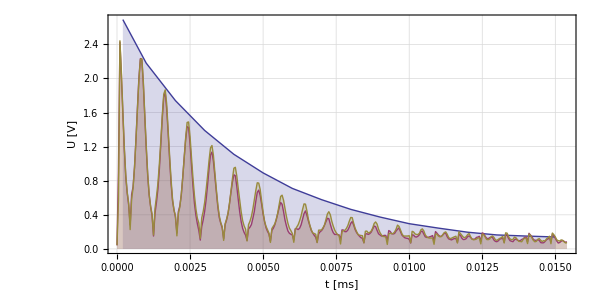

```mathematica
PlotSe2=Drop[Replace[SE02Mol,{t_,V_}->{2*t,V},2],-6];
Show[ListLinePlot[{PlotSe2,Drop[CP02Mol,-192],Drop[MG02Mol,-192]},PlotRange->All,Filling->Axis],niceStyle,AspectRatio->1.5/3,FrameLabel->{"t [ms]","U [V]"}]
```